```mathematica
Quit[]
```

### 1.1 some parameters

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\PythonTemp\NSPBGW\code00

```mathematica
Msun=1.98847*10^30;                      (* Mass of the sun*)
Mpc=3.085677581*10^22;               (* million par second *)
pc=3.085677581*10^16;                  (* parsecond *)
yt=365*3600*24;
ly=365*3600*24*c;                          (* light year *)
Mly=10^6*365*24*3600*c;          (* million light year *)
H0=67.9*10^3/Mpc;                    (* Hubble constant *)
c=299792458;                                 (* Speed of light *)
Gn=6.67408*10^-11;(* Gravitational constant *)
```

```mathematica
a1=3.916;        b1=4.078;             c1= 4.857;
a2=7.701;        b2= 7.587;            c2= 6.981;
a3=0.00858;   b3= 0.00839;        c3= 0.00706;
a4=0.22114;   b4= 0.21695;        c4= 0.19351;
a5=3.269;        b5= 3.614;            c5= 4.085;
a6=11.964;      b6= 11.942;         c6= 12.065;
a7=13.349;      b7= 13.751;         c7= 10.521;
a8=1.3683;      b8= 1.3373;         c8= 1.5905;
a9=3.254;        b9= 3.606;            c9= 4.104;
a10=−12.953; b10=−22.996;     c10=−28.726;
a11=0.9237;    b11= 1.6229;       c11= 2.0845;
a12=6.20;         b12= 4.88;           c12= 4.89;
a13=14.383;    b13= 14.274;       c13= 14.302;
a14=16.693;    b14= 23.560;       c14= 22.881;
a15=−1.0514; b15=−1.5564;     c15=−1.7690;
a16=2.486 ;     b16=2.095;          c16= 0.989;
a17=15.362 ;   b17=15.294;       c17= 15.313;
a18=0.085;      b18= 0.084;        c18= 0.091;
a19=6.23;        b19= 6.36;           c19= 4.68;
a20=11.68;      b20= 11.67;        c20= 11.65;
a21=−0.029;   b21=−0.042;      c21=−0.086;
a22=20.1;        b22= 14.8;           c22= 10.0;
a23=14.19;      b23= 14.18;        c23= 14.15;
ρs=7.86*10^3(*ρFe=7.86*10^3 kg/m^3*)
mn=1.4Msun(* the NS parameters*)
```

7860.

2.78386×10^30

### 1.2 the state of the NS, and give the relation between p and ρ

```mathematica
(*ra=10.74*10^3;*)
(*rb=11.74*10^3;*)
rc=12.57*10^3;
ξa=Log10[ρa1];
ks=(c1+c2 ξa+c3 ξa^3)/(1+c4 ξa)(Exp[c5(ξa-c6)]+1)^-1+(c7+c8 ξa)(Exp[c9(c6-ξa)]+1)^-1+(c10+c11 ξa)(Exp[c12(c13-ξa)]+1)^-1+(c14+c15 ξa)(Exp[c16(c17-ξa)]+1)^-1+c18(1+(c19(ξa-c20))^2)^-1+c21(1+(c22(ξa-c23))^2)^-1/.ρa1->10^-3 ρs;
ps=0.1*10^ks;
ζ[ρ_]:=(c1+c2 ξ[ρ]+c3 ξ[ρ]^3)/(1+c4 ξ[ρ])(Exp[c5(ξ[ρ]-c6)]+1)^-1+(c7+c8 ξ[ρ])(Exp[c9(c6-ξ[ρ])]+1)^-1+(c10+c11 ξ[ρ])(Exp[c12(c13-ξ[ρ])]+1)^-1+(c14+c15 ξ[ρ])(Exp[c16(c17-ξ[ρ])]+1)^-1+c18(1+(c19(ξ[ρ]-c20))^2)^-1+c21(1+(c22(ξ[ρ]-c23))^2)^-1
ξ[ρ_]:=Log10[10^-3 ρ];
pa[ρ_]:=10^ ζ[ρ]/10;
```

### 1.3 solve the result of the p,ρ,m from the equation

```mathematica
(* equation for the p,ρ,m*)
dpadρ[ρ_]:=Evaluate[D[pa[ρ],ρ]];
(*dpadr[r_]:=-(ρ[r]+pa[ρ[r]]/c^2)(Gn( m[r]+4π r^3 pa[ρ[r]]/c^2))/(r(r-2 Gn m[r]/c^2));*)
dpadr[r_]:=-(Gn m[r]ρ[r])/r^2;
dρdr[r_]:=dpadr[r] dpadρ[ρ[r]]^-1;
dmr[r_]:=4π r^2 ρ[r];
```

```mathematica
Res=Flatten[NDSolve[{m'[r]==dmr[r],ρ'[r]==dρdr[r],
ρ[10^-15]==0.928*10^14 ρs,m[10^-15]==0},{m,ρ},
{r,10^-15,12589.478339272455},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]];
```

```mathematica
m1[r_]=m[r]/.Res;
ρ1[r_]=ρ[r]/.Res;
dm1dr[r_]:=4π r^2 ρ1[r];
dρ1dr[r_]:=dpadr[r] dpadρ[ρ[r]]^-1/.Res;
p1[r_]:=pa[ρ1[r]];
```

```mathematica
Clear[m1,ρ1,p1]
```

```mathematica
(*ra=r/.FindRoot[ρ1[r]==7860,{r,rc}]*)
ra = 12589.478339307725;
```

```mathematica
{m1[ rc]/Msun,m1[ 12589.4]/Msun,ρ1[rc],ρ1[12589.47833927],ρ1[12589.478339307725]}
```

{1.39971,1.39971,3.00023×10^10,10112.7,7860.}

```mathematica
β1[r_]:=1/2 Log[(1-(2Gn m1[r])/(r c^2))^-1];
(*dα1dr[r_]:=(Gn (m1[r]+4π r^3 p1[r]/c^2))/(r^2 c^2(1-2Gn m1[r]/(r c^2)));*)
dα1dr[r_]:=(Gn (m1[r]))/(r^2 c^2);
(* the β1,B1 parameters can be directly calculate *)
B1[r_]:=(1-(2Gn m1[r])/(r c^2))^-1;
α1ra=1/2 Log[1-(2Gn m1[ra])/(ra c^2)]
NDSolve[{α'[r]==dα1dr[r],α[ra]==α1ra},{α},
{r,10^-10,ra},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
α1[r_]=α[r]/.%[[1,1]];
```

-0.355835

```mathematica
Export[ "model2alpha.txt", Table[N[{10^logr,α1[10^logr],dα1dr[10^logr]},16],{logr,-15,Log10[ra],20/100000}],"Table"]
Export[ "model2m.txt", Table[N[{10^logr,m1[10^logr],dm1dr[10^logr]},16],{logr,-15,Log10[ra],20/100000}],"Table"]
Export[ "model2rho.txt", Table[N[{10^logr,ρ1[10^logr],dρ1dr[10^logr]},16],{logr,-15,Log10[ra],20/100000}],"Table"]
```

$Aborted

$Aborted

$Aborted

```mathematica
Export[ "Newtonmodel2alpha.txt", Table[N[{10^logr,α1[10^logr],dα1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
Export[ "Newtonmodel2m.txt", Table[N[{10^logr,m1[10^logr],dm1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
Export[ "Newtonmodel2rho.txt", Table[N[{10^logr,ρ1[10^logr],dρ1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
```

Newtonmodel2alpha.txt

Newtonmodel2m.txt

Newtonmodel2rho.txt

```mathematica
Sort[{1.399708742724039,1.3997087429165107,3.0002318334381027*^10,10112.705150528009,7859.999832124393}]
```

{1.39971,1.39971,7860.,10112.7,3.00023×10^10}

```mathematica
rk=12589
ρk=ρ1[rk]
mk=m1[rk]
```

12589

8.53319×10^7

2.78328×10^30

```mathematica
Clear[rk,ρk,mk]
```

```mathematica
NDSolve[{m'[r]==dmr[r],ρ'[r]==dρdr[r],
ρ[rk]==ρk,m[rk]==mk},{m,ρ},
{r,0.01,rk},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
```

```mathematica
mk1[r_]=m[r]/.%[[1,1]];
ρk1[r_]=ρ[r]/.%%[[1,2]];
pk1[r_]:=pa[ρk1[r]];
(* test*)
```

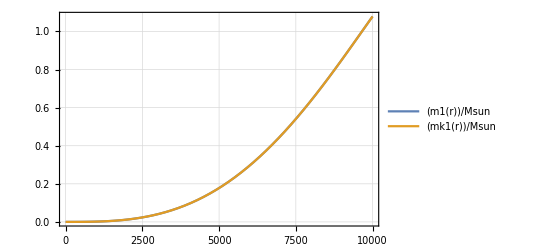

-Graphics-

-Graphics-

```mathematica
Plot[{m1[r]/Msun,mk1[r]/Msun},{r,1,10000},PlotTheme->"Detailed"]
Plot[{(*ρ1[r],*)ρk1[r]},{r,1,10000},PlotTheme->"Detailed"]
Plot[{p1[r],pk1[r]},{r,1,10000},PlotTheme->"Detailed"]
```

### 1.4 Solve the metric from the behind

{0.473306,0.473321,0.474827,0.518147,0.656937,0.65697}

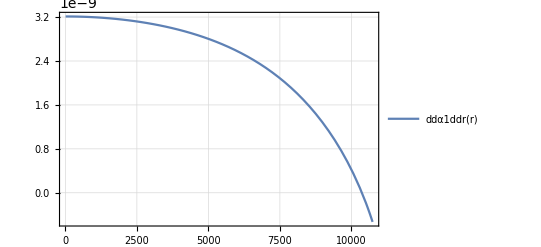

```mathematica
β1[r_]:=1/2 Log[(1-(2Gn m1[r])/(r c^2))^-1];
dα1dr[r_]:=(Gn (m1[r]+4π r^3 p1[r]/c^2))/(r^2 c^2(1-2Gn m1[r]/(r c^2)));
(* the β1,B1 parameters can be directly calculate *)
B1[r_]:=(1-(2Gn m1[r])/(r c^2))^-1;
α1ra=1/2 Log[1-(2Gn m1[ra])/(ra c^2)];
NDSolve[{α'[r]==dα1dr[r],α[ra]==α1ra},{α},
{r,10^-8,ra},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
α1[r_]=α[r]/.%[[1,1]];
A1[r_]:=Exp[2α1[r]];
{A1[10],A1[100],A1[1000],A1[ra/2],A1[ra-1],A1[ra]}
 ddα1ddr[r_]:=Evaluate[D[dα1dr[r],r]];
Plot[ddα1ddr[r],{r,10,10740},PlotRange->Full,PlotTheme->"Detailed"]
```

```mathematica
orbE[r_](*=ⅆt/ⅆτ A1[r]*)=√(A1[r]/(1-r dα1dr[r]))c^2;
doEdr[r_]=(-3  dα1dr[r]+2 r  dα1dr[r]^2-r  ddα1ddr[r])/(-2+2 r dα1dr[r])√(A1[r]/(1-r dα1dr[r]));
doEdt[t_]=doEdr[r[t]]r'[t] c^2;
cs1[r_]=(dpadρ[ρ1[r]])^(1/2);
ω1[r_]=c(dα1dr[r] A1[r]/r)^(1/2);
(* calculate the ω1[r]*)
```

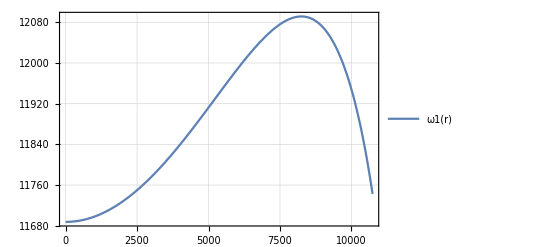

```mathematica
Plot[ω1[r],{r,1,10740},PlotRange->Full,PlotTheme->"Detailed"]
```

{0.473306,0.473321,0.474827,0.518147,0.656937,0.65697}

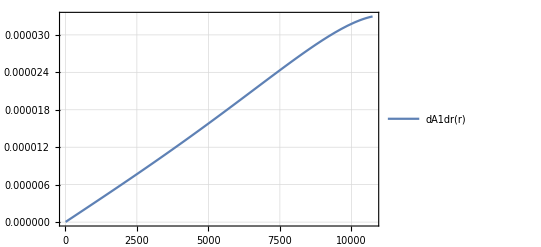

```mathematica
A1[r_]:=Exp[2α1[r]];
{A1[10],A1[100],A1[1000],A1[ra/2],A1[ra-1],A1[ra]}
 dA1dr[r_]:=Evaluate[D[A1[r],r]];
(* calculate the dA1[r]/dr*)
Plot[dA1dr[r],{r,10,10740},PlotRange->Full,PlotTheme->"Detailed"]
```

### 1.5 the moving for the result(1,10^-6)

```mathematica
orbE[r_](*=ⅆt/ⅆτ A1[r]*)=√(A1[r]/(1-r dα1dr[r]))c^2;
doEdr[r_]=(-3  dα1dr[r]+2 r  dα1dr[r]^2-r  ddα1ddr[r])/(-2+2 r dα1dr[r])√(A1[r]/(1-r dα1dr[r]));
doEdt[t_]=doEdr[r[t]]r'[t] c^2;
cs1[r_]=(dpadρ[ρ1[r]])^(1/2);
ω1[r_]=c(dα1dr[r] A1[r]/r)^(1/2);
v1[r_]=ω1[r]r;
calM[r_]=v1[r]/ cs1[r];
Iϕ1[r_]=Piecewise[{{0.7706Log[(1+calM[r])/(1.0004-0.9185calM[r])]-1.4703calM[r],calM[r]<1.0},{Log[3300(calM[r]-0.71)^5.72 calM[r]^-9.58],1.0<=calM[r]<4.4},{Log[10/(0.11calM[r]+1.65)],4.4<=calM[r]}}];
fr1[t_]=(*-(M*m[r])/(Mcs*r^2)*)(-4π ρ1[r[t]] Gn^2 mp[t]^2/v1[r[t]]^2)Iϕ1[r[t]];
λa=0.707;
dmpdt[t_]=4π λa ρ1[r[t]](Gn^2 mp[t]^2)/((cs1[r[t]]^2+v1[r[t]]^2)^(3/2));
gwdedt1[t_]=-(32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5)+1/(5 c^7)2Gn r[t]^4 mp[r[t]]^2 ω1[r[t]]^6(-16 r[t]^2 ω1[r[t]]^2+(16+24(A1[r[t]]-B1[r[t]])^2)(A1[r[t]]+1)/2)-(8Gn (ω1[r[t]] r[t])^2 r[t]^2 mp[r[t]]^2 ω1[r[t]]^6)/(45 c^7)-(2734Gn r[t]^6 mp[r[t]]^2 ω1[r[t]]^8)/(315 c^7);
gwdEdt0[t_]=-(32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5);
dEdtgfa[t_]=-dmpdt[t] v1[r[t]]^2;
dEdtgdf[t_]=fr1[t]v1[r[t]];
dϵdtgfa[t_]=-4π λa ρ1[r[t]](Gn^2 mp[t])/((cs1[r[t]]^2+v1[r[t]]^2)^(3/2)) v1[r[t]]^2;
dϵdtgdf[t_]=(-4π ρ1[r[t]] Gn^2 mp[t]/v1[r[t]]^2)Iϕ1[r[t]]v1[r[t]];
gwdϵdt0[t_]=-(32Gn r[t]^4 mp[t] ω1[r[t]]^6)/(5 c^5);
(* dϵ=dE/μ *)
NDSolve[{mp'[t]==dmpdt[t],r'[t]==(dϵdtgfa[t]+dϵdtgdf[t]+gwdϵdt0[t])/(doEdr[r[t]] c^2),r[0]==10000,mp[0]==10^-6 Msun},{mp,r},{t,0,111.07286},(*Method->{"EquationSimplification"->Automatic},*)(*Method->{"Extrapolation",Method->"ExplicitModifiedMidpoint"},*)(*Method->"StiffnessSwitching",*)MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
mp1[t_]=mp[t]/.%[[1,1]];
r1[t_]=r[t]/.%%[[1,2]];
```

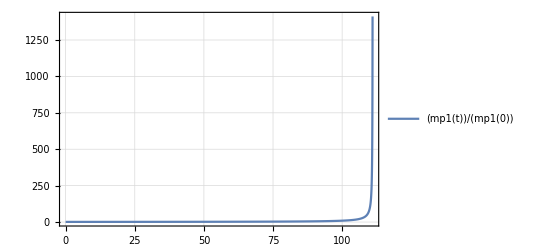

```mathematica
Plot[mp1[t]/mp1[0],{t,0,111},PlotRange->Full,PlotTheme->"Detailed"]
```

### 1.6 the moving for the result(2,10^-3)

```mathematica
orbE[r_](*=ⅆt/ⅆτ A1[r]*)=√(A1[r]/(1-r dα1dr[r]))c^2;
doEdr[r_]=(-3  dα1dr[r]+2 r  dα1dr[r]^2-r  ddα1ddr[r])/(-2+2 r dα1dr[r])√(A1[r]/(1-r dα1dr[r]));
doEdt[t_]=doEdr[r[t]]r'[t] c^2;
cs1[r_]=(dpadρ[ρ1[r]])^(1/2);
ω1[r_]=c(dα1dr[r] A1[r]/r)^(1/2);
v1[r_]=ω1[r]r;
calM[r_]=v1[r]/ cs1[r];
Iϕ1[r_]=Piecewise[{{0.7706Log[(1+calM[r])/(1.0004-0.9185calM[r])]-1.4703calM[r],calM[r]<1.0},{Log[3300(calM[r]-0.71)^5.72 calM[r]^-9.58],1.0<=calM[r]<4.4},{Log[10/(0.11calM[r]+1.65)],4.4<=calM[r]}}];
fr1[t_]=(*-(M*m[r])/(Mcs*r^2)*)(-4π ρ1[r[t]] Gn^2 mp[t]^2/v1[r[t]]^2)Iϕ1[r[t]];
λa=0.707;
dmpdt[t_]=4π λa ρ1[r[t]](Gn^2 mp[t]^2)/((cs1[r[t]]^2+v1[r[t]]^2)^(3/2));
gwdedt1[t_]=-(32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5)+1/(5 c^7)2Gn r[t]^4 mp[r[t]]^2 ω1[r[t]]^6(-16 r[t]^2 ω1[r[t]]^2+(16+24(A1[r[t]]-B1[r[t]])^2)(A1[r[t]]+1)/2)-(8Gn (ω1[r[t]] r[t])^2 r[t]^2 mp[r[t]]^2 ω1[r[t]]^6)/(45 c^7)-(2734Gn r[t]^6 mp[r[t]]^2 ω1[r[t]]^8)/(315 c^7);
gwdEdt0[t_]=-(32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5);
dEdtgfa[t_]=-dmpdt[t] v1[r[t]]^2;
dEdtgdf[t_]=fr1[t]v1[r[t]];
dϵdtgfa[t_]=-4π λa ρ1[r[t]](Gn^2 mp[t])/((cs1[r[t]]^2+v1[r[t]]^2)^(3/2)) v1[r[t]]^2;
dϵdtgdf[t_]=(-4π ρ1[r[t]] Gn^2 mp[t]/v1[r[t]]^2)Iϕ1[r[t]]v1[r[t]];
gwdϵdt0[t_]=-(32Gn r[t]^4 mp[t] ω1[r[t]]^6)/(5 c^5);
(* dϵ=dE/μ *)
NDSolve[{mp'[t]==dmpdt[t],r'[t]==(dϵdtgfa[t]+dϵdtgdf[t]+gwdϵdt0[t])/(doEdr[r[t]] c^2),r[0]==10000,mp[0]==10^-3 Msun},{mp,r},{t,0, 0.1255},(*Method->{"EquationSimplification"->Automatic},*)(*Method->{"Extrapolation",Method->"ExplicitModifiedMidpoint"},*)(*Method->"StiffnessSwitching",*)MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
mp2[t_]=mp[t]/.%[[1,1]];
r2[t_]=r[t]/.%%[[1,2]];
```

NDSolve::ndsz: 在 t == 0.125508 处，步长实际上为零；可能存在奇点或者刚性系统.

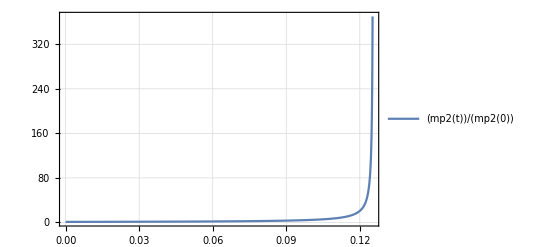

```mathematica
Plot[mp2[t]/mp2[0],{t,0,0.1252},PlotRange->Full,PlotTheme->"Detailed"]
```

### 1.6 the moving for the result(3,10^-4)

```mathematica
orbE[r_](*=ⅆt/ⅆτ A1[r]*)=√(A1[r]/(1-r dα1dr[r]))c^2;
doEdr[r_]=(-3  dα1dr[r]+2 r  dα1dr[r]^2-r  ddα1ddr[r])/(-2+2 r dα1dr[r])√(A1[r]/(1-r dα1dr[r]));
doEdt[t_]=doEdr[r[t]]r'[t] c^2;
cs1[r_]=(dpadρ[ρ1[r]])^(1/2);
ω1[r_]=c(dα1dr[r] A1[r]/r)^(1/2);
v1[r_]=ω1[r]r;
calM[r_]=v1[r]/ cs1[r];
Iϕ1[r_]=Piecewise[{{0.7706Log[(1+calM[r])/(1.0004-0.9185calM[r])]-1.4703calM[r],calM[r]<1.0},{Log[3300(calM[r]-0.71)^5.72 calM[r]^-9.58],1.0<=calM[r]<4.4},{Log[10/(0.11calM[r]+1.65)],4.4<=calM[r]}}];
fr1[t_]=(*-(M*m[r])/(Mcs*r^2)*)(-4π ρ1[r[t]] Gn^2 mp[t]^2/v1[r[t]]^2)Iϕ1[r[t]];
λa=0.707;
dmpdt[t_]=4π λa ρ1[r[t]](Gn^2 mp[t]^2)/((cs1[r[t]]^2+v1[r[t]]^2)^(3/2));
gwdedt1[t_]=-(32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5)+1/(5 c^7)2Gn r[t]^4 mp[r[t]]^2 ω1[r[t]]^6(-16 r[t]^2 ω1[r[t]]^2+(16+24(A1[r[t]]-B1[r[t]])^2)(A1[r[t]]+1)/2)-(8Gn (ω1[r[t]] r[t])^2 r[t]^2 mp[r[t]]^2 ω1[r[t]]^6)/(45 c^7)-(2734Gn r[t]^6 mp[r[t]]^2 ω1[r[t]]^8)/(315 c^7);
gwdEdt0[t_]=-(32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5);
dEdtgfa[t_]=-dmpdt[t] v1[r[t]]^2;
dEdtgdf[t_]=fr1[t]v1[r[t]];
dϵdtgfa[t_]=-4π λa ρ1[r[t]](Gn^2 mp[t])/((cs1[r[t]]^2+v1[r[t]]^2)^(3/2)) v1[r[t]]^2;
dϵdtgdf[t_]=(-4π ρ1[r[t]] Gn^2 mp[t]/v1[r[t]]^2)Iϕ1[r[t]]v1[r[t]];
gwdϵdt0[t_]=-(32Gn r[t]^4 mp[t] ω1[r[t]]^6)/(5 c^5);
(* dϵ=dE/μ *)
NDSolve[{mp'[t]==dmpdt[t],r'[t]==(dϵdtgfa[t]+dϵdtgdf[t]+gwdϵdt0[t])/(doEdr[r[t]] c^2),r[0]==10000,mp[0]==10^-4 Msun},{mp,r},{t,0, 1.25508},(*Method->{"EquationSimplification"->Automatic},*)(*Method->{"Extrapolation",Method->"ExplicitModifiedMidpoint"},*)(*Method->"StiffnessSwitching",*)MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
mp3[t_]=mp[t]/.%[[1,1]];
r3[t_]=r[t]/.%%[[1,2]];
```

NDSolve::ndsz: 在 t == 1.25508 处，步长实际上为零；可能存在奇点或者刚性系统.

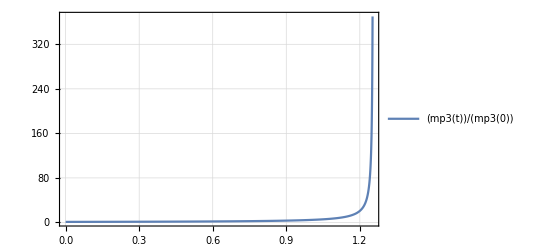

```mathematica
Plot[mp3[t]/mp3[0],{t,0,1.252},PlotRange->Full,PlotTheme->"Detailed"]
```

### 1.7 the moving for the result(4,10^-5)

```mathematica
orbE[r_](*=ⅆt/ⅆτ A1[r]*)=√(A1[r]/(1-r dα1dr[r]))c^2;
doEdr[r_]=(-3  dα1dr[r]+2 r  dα1dr[r]^2-r  ddα1ddr[r])/(-2+2 r dα1dr[r])√(A1[r]/(1-r dα1dr[r]));
doEdt[t_]=doEdr[r[t]]r'[t] c^2;
cs1[r_]=(dpadρ[ρ1[r]])^(1/2);
ω1[r_]=c(dα1dr[r] A1[r]/r)^(1/2);
v1[r_]=ω1[r]r;
calM[r_]=v1[r]/ cs1[r];
Iϕ1[r_]=Piecewise[{{0.7706Log[(1+calM[r])/(1.0004-0.9185calM[r])]-1.4703calM[r],calM[r]<1.0},{Log[3300(calM[r]-0.71)^5.72 calM[r]^-9.58],1.0<=calM[r]<4.4},{Log[10/(0.11calM[r]+1.65)],4.4<=calM[r]}}];
fr1[t_]=(*-(M*m[r])/(Mcs*r^2)*)(-4π ρ1[r[t]] Gn^2 mp[t]^2/v1[r[t]]^2)Iϕ1[r[t]];
λa=0.707;
dmpdt[t_]=4π λa ρ1[r[t]](Gn^2 mp[t]^2)/((cs1[r[t]]^2+v1[r[t]]^2)^(3/2));
gwdedt1[t_]=-(32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5)+1/(5 c^7)2Gn r[t]^4 mp[r[t]]^2 ω1[r[t]]^6(-16 r[t]^2 ω1[r[t]]^2+(16+24(A1[r[t]]-B1[r[t]])^2)(A1[r[t]]+1)/2)-(8Gn (ω1[r[t]] r[t])^2 r[t]^2 mp[r[t]]^2 ω1[r[t]]^6)/(45 c^7)-(2734Gn r[t]^6 mp[r[t]]^2 ω1[r[t]]^8)/(315 c^7);
gwdEdt0[t_]=-(32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5);
dEdtgfa[t_]=-dmpdt[t] v1[r[t]]^2;
dEdtgdf[t_]=fr1[t]v1[r[t]];
dϵdtgfa[t_]=-4π λa ρ1[r[t]](Gn^2 mp[t])/((cs1[r[t]]^2+v1[r[t]]^2)^(3/2)) v1[r[t]]^2;
dϵdtgdf[t_]=(-4π ρ1[r[t]] Gn^2 mp[t]/v1[r[t]]^2)Iϕ1[r[t]]v1[r[t]];
gwdϵdt0[t_]=-(32Gn r[t]^4 mp[t] ω1[r[t]]^6)/(5 c^5);
(* dϵ=dE/μ *)
NDSolve[{mp'[t]==dmpdt[t],r'[t]==(dϵdtgfa[t]+dϵdtgdf[t]+gwdϵdt0[t])/(doEdr[r[t]] c^2),r[0]==10000,mp[0]==10^-5 Msun},{mp,r},{t,0,12.5508},(*Method->{"EquationSimplification"->Automatic},*)(*Method->{"Extrapolation",Method->"ExplicitModifiedMidpoint"},*)(*Method->"StiffnessSwitching",*)MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
mp4[t_]=mp[t]/.%[[1,1]];
r4[t_]=r[t]/.%%[[1,2]];
```

NDSolve::ndsz: 在 t == 12.5508 处，步长实际上为零；可能存在奇点或者刚性系统.

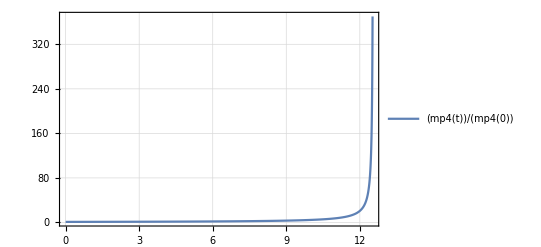

```mathematica
Plot[mp4[t]/mp4[0],{t,0,12.52},PlotRange->Full,PlotTheme->"Detailed"]
```